```mathematica
Get["G:\\LAT\\sd_metropolis\\convergence_analysis.m"];
(* Set of lattice parameters *)
lambdas={5.0, 4.0, 3.57, 3.45, 3.33, 3.23};
SourceNorms={0.0, 0.2540498,0.0,0.0,0.0,0.2733377};
VRdata={0.781, 0.708, 0.6499, 0.62134, 0.56809, 0.51202};
O0data={0.5577,0.6270,0.6590,0.66821,0.6775,0.6853};
O1data={0.4541,0.5464,0.5888,0.6009,0.6131,0.6234};
IncData={True,True,True,True,True,True};
(* Forming lists and plotting *)
GxPlots={}; mlPlots={};
For[iλ=1,iλ≤Length[lambdas],iλ++,
λ=lambdas[[iλ]];
SourceNorm = SourceNorms[[iλ]];
c=(iλ-1)/(Length[lambdas]-1);
Color1=RGBColor[c,0,1-c];
Color2=RGBColor[0.7+0.3c,0.7,0.7+0.3(1-c)];
(* Generating file names *)
ScalarFileName="G:\\LAT\\sd_metropolis\\data\\pcm_wc_mspace\\scalars_d2_t32_s32_l"<>fsndig[λ,4]<>".dat";
If[FileExistsQ[ScalarFileName],
Print["λ = ",λ,", ",ScalarFileName];
GxData=GetConvergenceData[ScalarFileName,1,2,1,1.0,12];
MeanLinkData=GetConvergenceData[ScalarFileName,1,4,1,1.0,12];
MeanLinkExactData={{0.0,1-VRdata[[iλ]]},{0.5,O1data[[iλ]]},{1.0,O0data[[iλ]]}};
NFactor=(1-O0data[[iλ]])/(1-MeanLinkData[[1,2]]);
GxData=LinearTransformColumn[GxData,2,1-NFactor,NFactor];
MeanLinkData=LinearTransformColumn[MeanLinkData,2,1-NFactor,NFactor];
MeanLinkData=LinearTransformColumn[MeanLinkData,3,0.0,NFactor];
Print["NFactor = ",NFactor];
Gr2=Show[PlotWithErrors[GxData,Color1],PlotLabel->"<Gx>"];
GrExact=ListPlot[MeanLinkExactData,PlotStyle->{Color2,PointSize[0.02]},PlotRange->{{0.0,All},{0.0,All}}];
Gr3=Show[GrExact,PlotWithErrors[MeanLinkData,Color1],PlotLabel->"<link>",DisplayFunction->$DisplayFunction];
GrUnFiltered=Show[Gr3,ImageSize->800];
Print[GrUnFiltered];
];
];
```

```mathematica
Print[Show[GrFiltered,GrUnFiltered,PlotStyle->{Red,Green}]]
```

λ = 3.23

a = 1., cc = 1., NN = 0.5

1 - NA = 9.12517×10^-6 +/- 5.4568×10^-6 (59.7994 %, 11579 points), G:\LAT\sd_metropolis\data\pcm_wc_mspace\scalars_d2_t32_s32_l3.2300_a1.00_c1.00_n0.50.dat

NFactor = 108183.

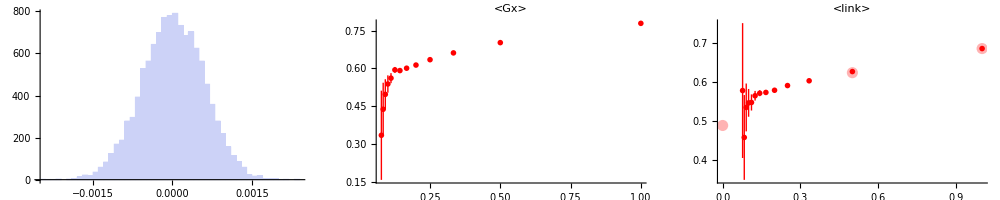

a = 1., cc = 1., NN = 0.8

1 - NA = 4.32995×10^-7 +/- 5.86868×10^-6 (1355.37 %, 10185 points), G:\LAT\sd_metropolis\data\pcm_wc_mspace\scalars_d2_t32_s32_l3.2300_a1.00_c1.00_n0.80.dat

NFactor = 49575.1

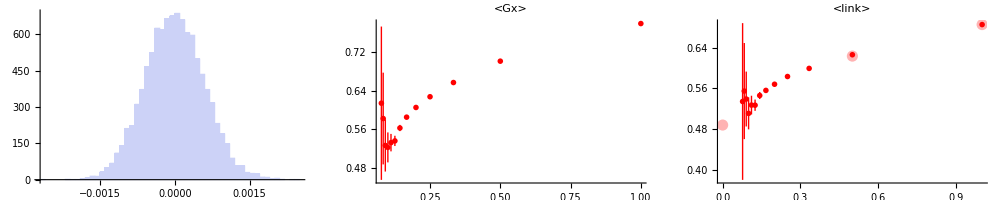

a = 1., cc = 1., NN = 1.

1 - NA = 0.0000107702 +/- 5.8898×10^-6 (54.6861 %, 9764 points), G:\LAT\sd_metropolis\data\pcm_wc_mspace\scalars_d2_t32_s32_l3.2300_a1.00_c1.00_n1.00.dat

NFactor = 36080.7

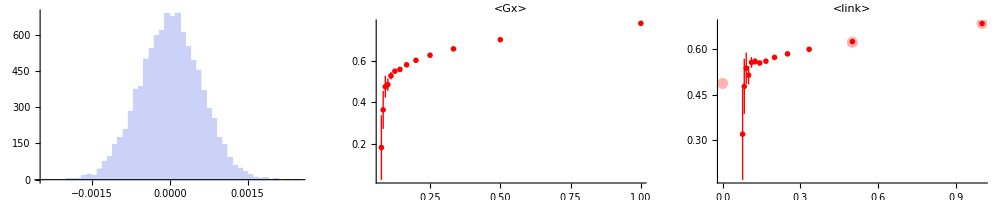

```mathematica
lambdas={5.0, 4.0, 3.57, 3.45, 3.33, 3.23};
VRdata={0.781, 0.708, 0.6499, 0.62134, 0.56809, 0.51202};
O0data={0.5577,0.6270,0.6590,0.66821,0.6775,0.6853};
O1data={0.4541,0.5464,0.5888,0.6009,0.6131,0.6234};
iλ=6;
λ=lambdas[[iλ]]; 
c=(iλ-1)/(Length[lambdas]-1);
Color1=RGBColor[c,0,1-c];
Color2=RGBColor[0.7+0.3c,0.7,0.7+0.3(1-c)];
Print["λ = ",λ];
Do[
(*Manipulate[*)
Print["a = ",a,", cc = ",cc,", NN = ",NN];
Suffix="d2_t32_s32_l"<>fsndig[λ,4]<>"_a"<>fsndig[a,2]<>"_c"<>fsndig[cc,2]<>"_n"<>fsndig[NN,2];
ScalarFileName="G:\\LAT\\sd_metropolis\\data\\pcm_wc_mspace\\scalars_"<>Suffix<>".dat";
MeanNAFileName="G:\\LAT\\sd_metropolis\\data\\pcm_wc_mspace\\mean_nA_"<>Suffix<>".dat";
If[FileExistsQ[ScalarFileName] && FileExistsQ[MeanNAFileName],
MeanNAData=Transpose[Import[MeanNAFileName,"Table"]][[1]];
Gr1=Histogram[MeanNAData];
MeanNA=Mean[MeanNAData]; ErrNA=√(Variance[MeanNAData]/(Length[MeanNAData]-1));
Print["1 - NA = ",MeanNA," +/- ",ErrNA," (", 100.0 ErrNA/MeanNA," %, ",Length[MeanNAData]," points), ",ScalarFileName];
GxData=GetConvergenceData[ScalarFileName,1,2,1,1.0,13];
MeanLinkData=GetConvergenceData[ScalarFileName,1,4,1,1.0,13];
NFactor=(1-O0data[[iλ]])/(1-MeanLinkData[[1,2]]);
GxData=LinearTransformColumn[GxData,2,1-NFactor,NFactor];
GxData=LinearTransformColumn[GxData,3,0.0,NFactor];
MeanLinkData=LinearTransformColumn[MeanLinkData,2,1-NFactor,NFactor];
MeanLinkData=LinearTransformColumn[MeanLinkData,3,0.0,NFactor];
Print["NFactor = ",NFactor];
MeanLinkExactData={{0.0,1-VRdata[[iλ]]},{0.5,O1data[[iλ]]},{1.0,O0data[[iλ]]}};
Gr2=Show[PlotWithErrors[GxData,Color1],PlotLabel->"<Gx>"];
GrExact=ListPlot[MeanLinkExactData,PlotStyle->{Color2,PointSize[0.02]},PlotRange->{{0.0,All},{0.0,All}}];
Gr3=Show[GrExact,PlotWithErrors[MeanLinkData,Color1],PlotLabel->"<link>"];
Print[GraphicsGrid[{{Gr1,Gr2,Gr3}},ImageSize->1000]],
0
];
(*,{a,{0.5,1.0,1.5}},{cc,{0.5,1.0,1.5}},{NN,{0.5,1.0,1.5}}*)
,{a,{1.0}},{cc,{1.0}},{NN,{0.5,0.8,1.0}}];
```

```mathematica
1+{1,2,3}
```

```mathematica
$HistoryLength=0;
MyLabel="";(*"_a1.00_c1.00_n0.50"*);
ScalarData=Import["G:\\LAT\\sd_metropolis\\data\\stereo_sm\\scalars_d2_t32_s32_l3.2300"<>MyLabel<>".dat","Table"];
MaxOrder=11;
MeanLinkFilteredData=Table[{},{MyOrder,0,MaxOrder}];
MeanLinkData=Table[{},{MyOrder,0,MaxOrder}];
For[i=1,i≤Length[ScalarData],i+=(MaxOrder+1),
If[ScalarData[[i,4]]<2,
For[MyOrder=0,MyOrder≤MaxOrder,MyOrder++,
AppendTo[MeanLinkFilteredData[[MyOrder+1]],ScalarData[[i+MyOrder,4]]];
];
];
For[MyOrder=0,MyOrder≤MaxOrder,MyOrder++,
AppendTo[MeanLinkData[[MyOrder+1]],ScalarData[[i+MyOrder,4]]];
];
];
ConvergenceData={};
ConvergenceFilteredData={};
NF=0.0;
For[MyOrder=0,MyOrder≤MaxOrder,MyOrder++,
Print["Order ", MyOrder,": ",Length[MeanLinkData[[MyOrder+1]]]," points in total, ",Length[MeanLinkFilteredData[[MyOrder+1]]]," filtered points"];
MeanFilteredLink=Mean[MeanLinkFilteredData[[MyOrder+1]]];
MeanLink=Mean[MeanLinkData[[MyOrder+1]]];
If[MyOrder==0,NFFiltered=(0.68563-1)/MeanFilteredLink;NF=(0.68563-1)/MeanLink];
Print["Mean Link: ", MeanLink,", Filtered Mean Link ",MeanFilteredLink];
Print["NF: ",NF,", NF Filtered: ",NFFiltered];

AppendTo[ConvergenceData,{1/(MyOrder+1),1+NF MeanLink}];
AppendTo[ConvergenceFilteredData,{1/(MyOrder+1),1+NFFiltered MeanFilteredLink}];
Print[Histogram[{MeanLinkData[[MyOrder+1]],MeanLinkFilteredData[[MyOrder+1]]},ChartStyle->{Opacity[0.5]}]];
Print[Histogram[MeanLinkFilteredData[[MyOrder+1]]]];
];
ListPlot[{ConvergenceData,ConvergenceFilteredData},PlotRange->{{0.0,All},All},PlotStyle->{{Red,PointSize[0.02]},{Blue,PointSize[0.02]}},PlotLabel->MyLabel]
```